# The Bethe Ansatz Solution of the triple box system: the wave function

```mathematica
Import["/Users/irina 1/qsu_repo/bethe_ansatz/TripleBox.png"]
```

-Graphics-

## Initialization

```mathematica
Needs["Combinatorica`"]
```

```mathematica
(* Subscript: Ctr + - *)
```

```mathematica
(* Power: Ctr + 6*)
```

```mathematica
(* Fraction: Ctr + / *)
```

```mathematica
vars = {x1,x2}
moms = {k1,k2}
Protect[vars]
```

Set::wrsym: Symbol vars is Protected.

{x1,x2}

{k1,k2}

{}

```mathematica
$Assumptions=And[And@@(#∈Reals &/@ {k1,k2,k3}),And@@(#>=0 &/@ {k1,k2,k3}), c ≥ 0, m >0, ℏ>0, L > 0, α ∈ Reals, β∈ Reals, xL∈Reals, xR∈ Reals]
```

k1∈Reals&&k2∈Reals&&k3∈Reals&&k1≥0&&k2≥0&&k3≥0&&c≥0&&m>0&&ℏ>0&&L>0&&α∈Reals&&β∈Reals&&xL∈Reals&&xR∈Reals

```mathematica
k1∈Reals&&k2∈Reals&&k3∈Reals&&k1≥0&&k2≥0&&k3≥0&&c≥0&&m>0&&ℏ>0&&L>0&&α∈Reals&&β∈Reals&&xL∈Reals&&xR∈Reals
```

k1∈Reals&&k2∈Reals&&k3∈Reals&&k1≥0&&k2≥0&&k3≥0&&c≥0&&m>0&&ℏ>0&&L>0&&α∈Reals&&β∈Reals&&xL∈Reals&&xR∈Reals

```mathematica
δ[x_] := DiracDelta[x]
```

```mathematica
(* Triangular product *)
```

```mathematica
Π̃[𝒦_, n_, X_, l_, u_] := ∏_(j=l+1)^u ∏_(k=l)^(j-1) 𝒦[n,X[[j]], X[[k]]]
Π̃[𝒦, 1,vars, 2, 5]
```

Part::partw: Part 3 of {x1, x2} does not exist.

Part::partw: Part 4 of {x1, x2} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

𝒦[1,{x1,x2}⟦3⟧,x2] 𝒦[1,{x1,x2}⟦4⟧,x2] 𝒦[1,{x1,x2}⟦4⟧,{x1,x2}⟦3⟧] 𝒦[1,{x1,x2}⟦5⟧,x2] 𝒦[1,{x1,x2}⟦5⟧,{x1,x2}⟦3⟧] 𝒦[1,{x1,x2}⟦5⟧,{x1,x2}⟦4⟧]

## The Full Hamiltonian

#### Kinetic term

```mathematica
kineticTerm[ψ_, X_] := Module[{N}, N=Length[X]; -ℏ^2/(2m)(∑_(j=1)^N D[D[ψ@@X, X[[j]]],X[[j]]]) ]
kineticTerm[f, vars]
```

-(ℏ^2 (f^(0,2)[x1,x2]+f^(2,0)[x1,x2]))/(2 m)

#### Interaction term

```mathematica
interTerm[ψ_, X_] := Module[{N, y}, (N=Length[X];  2 c*ψ@@X*∑_(j=1)^N ∑_(i=j+1)^N δ[X[[j]]-X[[i]]]  )]
interTerm[f, vars]
```

2 c DiracDelta[x1-x2] f[x1,x2]

#### External potential

```mathematica
(* The hard walls will be accounted for in the boundary conditions *)
```

```mathematica
barrierTerm[ψ_, X_, xa_,xb_] := Module[{N}, N=Length[X]; (α(∑_(j=1)^N δ[X[[j]]- xa])+ β(∑_(j=1)^N δ[X[[j]]- xb]))ψ@@X ]
barrierTerm[f, vars, xL]
```

barrierTerm[f,{x1,x2},xL]

```mathematica
barrierTerm[f,{x1,x2},xL]
```

barrierTerm[f,{x1,x2},xL]

```mathematica
barrierTerm[f,{x1,x2},xL, xR]
```

(α (DiracDelta[x1-xL]+DiracDelta[x2-xL])+β (DiracDelta[x1-xR]+DiracDelta[x2-xR])) f[x1,x2]

```mathematica
(α (DiracDelta[x1-xL]+DiracDelta[x2-xL])+β (DiracDelta[x1-xR]+DiracDelta[x2-xR])) f[x1,x2]
```

(α (DiracDelta[x1-xL]+DiracDelta[x2-xL])+β (DiracDelta[x1-xR]+DiracDelta[x2-xR])) f[x1,x2]

#### The Hamiltonian

```mathematica
ℋ[ψ_, X_] := kineticTerm[ψ, X] + interTerm[ψ, X] + barrierTerm[ψ, X, xa,xb]
ℋ[f, vars]
```

2 c DiracDelta[x1-x2] f[x1,x2]+(α (DiracDelta[x1-xa]+DiracDelta[x2-xa])+β (DiracDelta[x1-xb]+DiracDelta[x2-xb])) f[x1,x2]-(ℏ^2 (f^(0,2)[x1,x2]+f^(2,0)[x1,x2]))/(2 m)

### Define the wavefunction in all regions with n_L particles in the left trap and n_R particles in the right trap

### Basic wave function in the region (n_L, n_R)

```mathematica
(*(-1)^SignaturePermutation[Q[[np]]]*)
```

```mathematica
χ[nL_, nR_,x__] := Module[{Q, K, Nx, Ep}, (Nx = Length[{x}]; K = Symbol["k"<>ToString[#]]&/@Range[1, Nx];Q = Permutations[Range[1, Nx]];Ep = Tuples[{1,-1},Nx]; ∑_(ne=1)^(Dimensions[Ep][[1]]) ∑_(np=1)^(Dimensions[Q][[1]]) Subscript["𝒜", ToString[nL],ToString[nR]][ToString[Ep[[ne]]K[[Q[[np]]]]]]Exp[ⅈ∑_(j=1)^Nx Ep[[ne]][[j]]K[[Q[[np]][[j]]]]{x}[[j]]])]
Dimensions[χ@@Flatten[{nL,nR,vars}]]
χ@@Flatten[{nL, nR,vars}]
```

{8}

ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(nL,nR)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(nL,nR)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(nL,nR)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(nL,nR)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(nL,nR)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(nL,nR)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(nL,nR)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(nL,nR)[{k2, k1}]

```mathematica
(* Generate the list of all possible coefficients *)
generateCoefList[X_] := Module[{K, Nx, Ep, PP, nL, nR, curP}, (Nx = Length[X]; K = Permutations[Symbol["k"<>ToString[#]]&/@Range[1, Nx]];Ep = Tuples[{1,-1},Nx]; 
PP = Flatten[Outer[Times, K, Ep, 1],1];Flatten[(curP=#;(nL=#;(nR = #;Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[curP]])&/@Range[0, Nx-nL])&/@Range[0, Nx])&/@ PP])]
generateCoefList[vars][[1;;20]]
```

{𝒜_(0,0)[{k1, k2}],𝒜_(0,1)[{k1, k2}],𝒜_(0,2)[{k1, k2}],𝒜_(1,0)[{k1, k2}],𝒜_(1,1)[{k1, k2}],𝒜_(2,0)[{k1, k2}],𝒜_(0,0)[{k1, -k2}],𝒜_(0,1)[{k1, -k2}],𝒜_(0,2)[{k1, -k2}],𝒜_(1,0)[{k1, -k2}],𝒜_(1,1)[{k1, -k2}],𝒜_(2,0)[{k1, -k2}],𝒜_(0,0)[{-k1, k2}],𝒜_(0,1)[{-k1, k2}],𝒜_(0,2)[{-k1, k2}],𝒜_(1,0)[{-k1, k2}],𝒜_(1,1)[{-k1, k2}],𝒜_(2,0)[{-k1, k2}],𝒜_(0,0)[{-k1, -k2}],𝒜_(0,1)[{-k1, -k2}]}

```mathematica
(* Generate the list of all possible plain waves *)
generatePlainWaveList[X_] := Module[{K, Nx, Ep, PP, nL, nR, curP}, (Nx = Length[X]; K = Permutations[Symbol["k"<>ToString[#]]&/@Range[1, Nx]];Ep = Tuples[{1,-1},Nx]; 
PP = Flatten[Outer[Times, K, Ep, 1],1];Flatten[(Exp[ⅈ ∑_(j=1)^Nx #[[j]]X[[j]]])&/@ PP])]
generatePlainWaveList[{x1,x2,x3}]
```

{ⅇ^(ⅈ (k1 x1+k2 x2+k3 x3)),ⅇ^(ⅈ (k1 x1+k2 x2-k3 x3)),ⅇ^(ⅈ (k1 x1-k2 x2+k3 x3)),ⅇ^(ⅈ (k1 x1-k2 x2-k3 x3)),ⅇ^(ⅈ (-k1 x1+k2 x2+k3 x3)),ⅇ^(ⅈ (-k1 x1+k2 x2-k3 x3)),ⅇ^(ⅈ (-k1 x1-k2 x2+k3 x3)),ⅇ^(ⅈ (-k1 x1-k2 x2-k3 x3)),ⅇ^(ⅈ (k1 x1+k3 x2+k2 x3)),ⅇ^(ⅈ (k1 x1+k3 x2-k2 x3)),ⅇ^(ⅈ (k1 x1-k3 x2+k2 x3)),ⅇ^(ⅈ (k1 x1-k3 x2-k2 x3)),ⅇ^(ⅈ (-k1 x1+k3 x2+k2 x3)),ⅇ^(ⅈ (-k1 x1+k3 x2-k2 x3)),ⅇ^(ⅈ (-k1 x1-k3 x2+k2 x3)),ⅇ^(ⅈ (-k1 x1-k3 x2-k2 x3)),ⅇ^(ⅈ (k2 x1+k1 x2+k3 x3)),ⅇ^(ⅈ (k2 x1+k1 x2-k3 x3)),ⅇ^(ⅈ (k2 x1-k1 x2+k3 x3)),ⅇ^(ⅈ (k2 x1-k1 x2-k3 x3)),ⅇ^(ⅈ (-k2 x1+k1 x2+k3 x3)),ⅇ^(ⅈ (-k2 x1+k1 x2-k3 x3)),ⅇ^(ⅈ (-k2 x1-k1 x2+k3 x3)),ⅇ^(ⅈ (-k2 x1-k1 x2-k3 x3)),ⅇ^(ⅈ (k2 x1+k3 x2+k1 x3)),ⅇ^(ⅈ (k2 x1+k3 x2-k1 x3)),ⅇ^(ⅈ (k2 x1-k3 x2+k1 x3)),ⅇ^(ⅈ (k2 x1-k3 x2-k1 x3)),ⅇ^(ⅈ (-k2 x1+k3 x2+k1 x3)),ⅇ^(ⅈ (-k2 x1+k3 x2-k1 x3)),ⅇ^(ⅈ (-k2 x1-k3 x2+k1 x3)),ⅇ^(ⅈ (-k2 x1-k3 x2-k1 x3)),ⅇ^(ⅈ (k3 x1+k1 x2+k2 x3)),ⅇ^(ⅈ (k3 x1+k1 x2-k2 x3)),ⅇ^(ⅈ (k3 x1-k1 x2+k2 x3)),ⅇ^(ⅈ (k3 x1-k1 x2-k2 x3)),ⅇ^(ⅈ (-k3 x1+k1 x2+k2 x3)),ⅇ^(ⅈ (-k3 x1+k1 x2-k2 x3)),ⅇ^(ⅈ (-k3 x1-k1 x2+k2 x3)),ⅇ^(ⅈ (-k3 x1-k1 x2-k2 x3)),ⅇ^(ⅈ (k3 x1+k2 x2+k1 x3)),ⅇ^(ⅈ (k3 x1+k2 x2-k1 x3)),ⅇ^(ⅈ (k3 x1-k2 x2+k1 x3)),ⅇ^(ⅈ (k3 x1-k2 x2-k1 x3)),ⅇ^(ⅈ (-k3 x1+k2 x2+k1 x3)),ⅇ^(ⅈ (-k3 x1+k2 x2-k1 x3)),ⅇ^(ⅈ (-k3 x1-k2 x2+k1 x3)),ⅇ^(ⅈ (-k3 x1-k2 x2-k1 x3))}

```mathematica
funcOne[y_]:=1;
```

```mathematica
Ψ[x__] := Module[{nL, nR}, (Product[HeavisideTheta[{x}[[i]]-{x}[[i-1]]], {i, 2, Length[{x}]}]∑_(nL=0)^Length[{x}] ∑_(nR=0)^(Length[{x}] - nL) χ@@Flatten[{nL, nR, {x}}]Product[HeavisideTheta[xL-{x}[[i]]], {i, 1, nL}]Product[HeavisideTheta[xR-{x}[[i]]]HeavisideTheta[{x}[[i]]-xL], {i, nL+1, Length[{x}]-nR}]Product[HeavisideTheta[{x}[[i]]-xR], {i, Length[{x}]-nR+1, Length[{x}]}])]
Ψ@@vars
```

HeavisideTheta[-x1+x2] (HeavisideTheta[x1-xL] HeavisideTheta[x2-xL] HeavisideTheta[-x1+xR] HeavisideTheta[-x2+xR] (ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(0,0)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(0,0)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(0,0)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(0,0)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(0,0)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(0,0)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(0,0)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(0,0)[{k2, k1}])+HeavisideTheta[x1-xL] HeavisideTheta[x2-xR] HeavisideTheta[-x1+xR] (ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(0,1)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(0,1)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(0,1)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(0,1)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(0,1)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(0,1)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(0,1)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(0,1)[{k2, k1}])+HeavisideTheta[x1-xR] HeavisideTheta[x2-xR] (ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(0,2)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(0,2)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(0,2)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(0,2)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(0,2)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(0,2)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(0,2)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(0,2)[{k2, k1}])+HeavisideTheta[x2-xL] HeavisideTheta[-x1+xL] HeavisideTheta[-x2+xR] (ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(1,0)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(1,0)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(1,0)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(1,0)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(1,0)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(1,0)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(1,0)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(1,0)[{k2, k1}])+HeavisideTheta[-x1+xL] HeavisideTheta[x2-xR] (ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(1,1)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(1,1)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(1,1)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(1,1)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(1,1)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(1,1)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(1,1)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(1,1)[{k2, k1}])+HeavisideTheta[-x1+xL] HeavisideTheta[-x2+xL] (ⅇ^(ⅈ (-k1 x1-k2 x2)) 𝒜_(2,0)[{-k1, -k2}]+ⅇ^(ⅈ (-k1 x1+k2 x2)) 𝒜_(2,0)[{-k1, k2}]+ⅇ^(ⅈ (k1 x1-k2 x2)) 𝒜_(2,0)[{k1, -k2}]+ⅇ^(ⅈ (k1 x1+k2 x2)) 𝒜_(2,0)[{k1, k2}]+ⅇ^(ⅈ (-k2 x1-k1 x2)) 𝒜_(2,0)[{-k2, -k1}]+ⅇ^(ⅈ (-k2 x1+k1 x2)) 𝒜_(2,0)[{-k2, k1}]+ⅇ^(ⅈ (k2 x1-k1 x2)) 𝒜_(2,0)[{k2, -k1}]+ⅇ^(ⅈ (k2 x1+k1 x2)) 𝒜_(2,0)[{k2, k1}]))

### Two-particle scattering

```mathematica
(* The particles can scatter if they are in the same trap and if there are more than 2 of them there. *)
```

```mathematica
(* Swap momenta at specified positions *)
```

```mathematica
swapMom[p_, swapP_] := Module[{},(Flatten[{p[[1;;swapP[[1]]-1]], p[[swapP[[2]]]], p[[swapP[[1]]+1;;swapP[[2]]-1]], p[[swapP[[1]]]], p[[swapP[[2]]+1;;Dimensions[p][[1]]]]}])]
swapMom[{1,2, 3}, {1,3}]
```

{3,2,1}

```mathematica
(* Make swap rule for swapP swap and momenta permutations set relP. Only the rules which reduce iversions are allowed*)
swapRule[relP_, swapP_, nL_, nR_] := Module[{K, Ktemp},(K =Symbol["k"<>ToString[#]]&/@ Range[1, Length[relP[[1]]]];Flatten[(Ktemp = Sign[#]K[[Abs[#]]];If[Inversions[Abs[#]]<Inversions[swapMom[Abs[#], swapP]],(Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[swapMom[Ktemp, swapP]]]-> (Ktemp[[swapP[[2]]]]-Ktemp[[swapP[[1]]]] + ⅈ (c m)/ℏ^2)/(Ktemp[[swapP[[2]]]]-Ktemp[[swapP[[1]]]] - ⅈ (c m)/ℏ^2)*Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[Ktemp]]), (
{})])&/@relP])]
swapRule[{{1,2, 3}, {2, 3,1}, {3,2,1}}, {1,3}, 3, 0]
```

{𝒜_(3,0)[{k3, k2, k1}]→((-k1+k3+(ⅈ c m)/ℏ^2) 𝒜_(3,0)[{k1, k2, k3}])/(-k1+k3-(ⅈ c m)/ℏ^2)}

```mathematica
(* make subset of the permutation set P, where elements are not swapP swaps of each other *)
swapAllMom[P_, swapP_] := Module[{tP}, (tP = {};(If[!MemberQ[tP,swapMom[#, swapP]],(tP= Append[tP, Flatten[#]];#), {}]) &/@ P)]/.{}->Sequence[]
swapAllMom[{{k1,k2,k3}, {k3, k2, k1}, {k2, k1, k3}}, {1,2}]
```

{{k1,k2,k3},{k3,k2,k1}}

```mathematica
(* Generate base scattering permutations (the ones that will not be substituted) *)
generateBaseScatter[partDistr_, wellNum_] := Module[{rN,N, Sbase,  Srest,Srest1, Sres2, Prest, Prest1,Prest2, Pbase, moms},(
N=Total[partDistr]; 
rN = Range[1, N];
If[partDistr[[wellNum]] > 1,
( Sbase = Subsets[rN, {partDistr[[wellNum]]}];
Pbase = Sbase;
(*Pbase = ((Symbol["k"<>ToString[#]])&/@ #) &/@ Sbase ;*)
 Srest = Complement[rN, #] &/@ Sbase;
Prest = Srest;
 (*Prest = ((Symbol["k"<>ToString[#]])&/@ #) &/@ Srest ;*)
Prest1 = Permutations[#]&/@Prest;
If[wellNum ≠ 2, 
(
If[wellNum == 1,
(
moms=Flatten[Outer[Join, {Pbase[[#]]}, Prest1[[#]], 1]&/@ Range[1, Length[Pbase]], 2]
),
(
moms = Flatten[Outer[Join, Prest1[[#]],{Pbase[[#]]}, 1]&/@ Range[1, Length[Pbase]], 2]
)]
),
(
Prest2 = ((#[[partDistr[[wellNum-1]]+ 1 ;; N-partDistr[[wellNum]]]])&/@ #) &/@ Prest1;
Prest1 = ((#[[1 ;; partDistr[[wellNum -1]]]])&/@ #) &/@ Prest1;
moms = Flatten[Outer[Join, Prest1[[#]],{Pbase[[#]]}, 1]&/@ Range[1, Length[Pbase]], 2];
moms = (Join[moms[[#]], Flatten[Prest2, 1][[#]]]) &/@ Range[1, Dimensions[moms][[1]]]
)]
) ]
)]
generateBaseScatter[{2,2,2}, 3][[1;;10]]
```

{{3,4,5,6,1,2},{3,4,6,5,1,2},{3,5,4,6,1,2},{3,5,6,4,1,2},{3,6,4,5,1,2},{3,6,5,4,1,2},{4,3,5,6,1,2},{4,3,6,5,1,2},{4,5,3,6,1,2},{4,5,6,3,1,2}}

```mathematica
(* Generate scattering permutations which will have to applied recursively *)
generateRecursiveScatter[partDistr_] := Module[{rN,N,P, S}, 
(N=Total[partDistr]; 
rN = Range[1, N];
P= Permutations[rN](*;
S = Subsets[Range[1,partDistr[[1]]], {2}];
S = Join[S, Subsets[Range[partDistr[[1]]+1, N-partDistr[[3]]], {2}]];
S = Join[S,  Subsets[Range[ N-partDistr[[3]]+1, N], {2}]];
swapAllMom[P, #]&/@ S*)
)]
generateRecursiveScatter[{2,2,2}][[1;;10]]
```

{{1,2,3,4,5,6},{1,2,3,4,6,5},{1,2,3,5,4,6},{1,2,3,5,6,4},{1,2,3,6,4,5},{1,2,3,6,5,4},{1,2,4,3,5,6},{1,2,4,3,6,5},{1,2,4,5,3,6},{1,2,4,5,6,3}}

```mathematica
generateAdjSwaps[from_, to_]:={#, #+1} &/@Range[from, to-1]
generateAdjSwaps[2,5]
```

{{2,3},{3,4},{4,5}}

#### Scattering in the left trap

```mathematica
(* Scattering in one block *)
scatterLeftOneBlock[X_, nL_, nR_] := Module[{S,P, Ep, PP}, If[nL>1,(S = generateAdjSwaps[1, nL]; P= generateRecursiveScatter[{nL, Length[X]-nR-nL, nR}];(*generateBaseScatter[{nL, Length[X]-nR-nL, nR}, 1];*)Ep = Tuples[{1,-1}, Length[X]];
PP = Flatten[Outer[Times, P, Ep, 1],1]; Flatten[(swapRule[PP, #, nL, nR])&/@S]), {}]]
scatterLeftOneBlock[vars, Length[vars], 0]
```

{𝒜_(2,0)[{k2, k1}]→((-k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{k1, k2}])/(-k1+k2-(ⅈ c m)/ℏ^2),𝒜_(2,0)[{-k2, k1}]→((-k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{k1, -k2}])/(-k1-k2-(ⅈ c m)/ℏ^2),𝒜_(2,0)[{k2, -k1}]→((k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{-k1, k2}])/(k1+k2-(ⅈ c m)/ℏ^2),𝒜_(2,0)[{-k2, -k1}]→((k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{-k1, -k2}])/(k1-k2-(ⅈ c m)/ℏ^2)}

```mathematica
scatterLeft[vars_] := Module[{nL, nR}, (Flatten[(nL = #;(nR = #;scatterLeftOneBlock[vars, nL, nR])&/@ Range[0, Length[vars]-nL])&/@ Range[0, Length[vars]]])]
scatterLeft[vars]
```

{𝒜_(2,0)[{k2, k1}]→((-k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{k1, k2}])/(-k1+k2-(ⅈ c m)/ℏ^2),𝒜_(2,0)[{-k2, k1}]→((-k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{k1, -k2}])/(-k1-k2-(ⅈ c m)/ℏ^2),𝒜_(2,0)[{k2, -k1}]→((k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{-k1, k2}])/(k1+k2-(ⅈ c m)/ℏ^2),𝒜_(2,0)[{-k2, -k1}]→((k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(2,0)[{-k1, -k2}])/(k1-k2-(ⅈ c m)/ℏ^2)}

#### Scattering in the right trap

```mathematica
(* Scattering in one block *)
scatterRightOneBlock[X_, nL_, nR_] := Module[{S,P, Ep, PP}, If[nR>1,(S = generateAdjSwaps[Length[X]-nR+1, Length[X]]; P= generateRecursiveScatter[{nL, Length[X]-nR-nL, nR}];(*generateBaseScatter[{nL, Length[X]-nR-nL, nR}, 1];*)Ep = Tuples[{1,-1}, Length[X]];
PP = Flatten[Outer[Times, P, Ep, 1],1]; Flatten[(swapRule[PP, #, nL, nR])&/@S]), {}]]
scatterRightOneBlock[vars, 0,Length[vars]]
```

{𝒜_(0,2)[{k2, k1}]→((-k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{k1, k2}])/(-k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,2)[{-k2, k1}]→((-k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{k1, -k2}])/(-k1-k2-(ⅈ c m)/ℏ^2),𝒜_(0,2)[{k2, -k1}]→((k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{-k1, k2}])/(k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,2)[{-k2, -k1}]→((k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{-k1, -k2}])/(k1-k2-(ⅈ c m)/ℏ^2)}

```mathematica
scatterRight[vars_] := Module[{nL, nR}, (Flatten[(nL = #;(nR = #;scatterRightOneBlock[vars, nL, nR])&/@ Range[0, Length[vars]-nL])&/@ Range[0, Length[vars]]])]
scatterRight[vars]
```

{𝒜_(0,2)[{k2, k1}]→((-k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{k1, k2}])/(-k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,2)[{-k2, k1}]→((-k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{k1, -k2}])/(-k1-k2-(ⅈ c m)/ℏ^2),𝒜_(0,2)[{k2, -k1}]→((k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{-k1, k2}])/(k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,2)[{-k2, -k1}]→((k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,2)[{-k1, -k2}])/(k1-k2-(ⅈ c m)/ℏ^2)}

#### Scattering in the middle trap

```mathematica
(* Scattering in one block *)
scatterMiddleOneBlock[X_, nL_, nR_] := Module[{S,P, Ep, PP}, If[Length[X] - nR - nL>1,(S = generateAdjSwaps[nL+1, Length[X]-nR]; P= generateRecursiveScatter[{nL, Length[X]-nR-nL, nR}];(*generateBaseScatter[{nL, Length[X]-nR-nL, nR}, 1];*)Ep = Tuples[{1,-1}, Length[X]];
PP = Flatten[Outer[Times, P, Ep, 1],1]; Flatten[(swapRule[PP, #, nL, nR])&/@S]), {}]]
scatterMiddleOneBlock[vars, 0,0]
```

{𝒜_(0,0)[{k2, k1}]→((-k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{k1, k2}])/(-k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,0)[{-k2, k1}]→((-k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{k1, -k2}])/(-k1-k2-(ⅈ c m)/ℏ^2),𝒜_(0,0)[{k2, -k1}]→((k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{-k1, k2}])/(k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,0)[{-k2, -k1}]→((k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{-k1, -k2}])/(k1-k2-(ⅈ c m)/ℏ^2)}

```mathematica
scatterMiddle[vars_] := Module[{nL, nR}, (Flatten[(nL = #;(nR = #;scatterMiddleOneBlock[vars, nL, nR])&/@ Range[0, Length[vars]-nL])&/@ Range[0, Length[vars]]])]
scatterMiddle[vars]
```

{𝒜_(0,0)[{k2, k1}]→((-k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{k1, k2}])/(-k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,0)[{-k2, k1}]→((-k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{k1, -k2}])/(-k1-k2-(ⅈ c m)/ℏ^2),𝒜_(0,0)[{k2, -k1}]→((k1+k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{-k1, k2}])/(k1+k2-(ⅈ c m)/ℏ^2),𝒜_(0,0)[{-k2, -k1}]→((k1-k2+(ⅈ c m)/ℏ^2) 𝒜_(0,0)[{-k1, -k2}])/(k1-k2-(ⅈ c m)/ℏ^2)}

### Reflection

```mathematica
(* If the leftmost (rightmost) particle which is in the left (right) trap reflects agains the left wall -> its momentum is inversed *)
```

#### Left reflection

```mathematica
(* General condition for reflection of the pNum's particle from the left wall. Does not yet check for number of particles in the left well. L is the length of the whole system from one wall to another *)
leftReflectionGen[X_, nL_, nR_, L_, pNum_] :=Module[{Epp,P,Epm,PP,PM, K}, (P= Permutations[Symbol["k"<>ToString[#]]&/@Range[1, Length[X]]];
Epp = DeleteDuplicates[Flatten[{#[[1;;pNum-1]],1, #[[pNum+1;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];
 Epm =DeleteDuplicates[Flatten[{#[[1;;pNum-1]],-1, #[[pNum+1;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];
(*Epp = DeleteDuplicates[Flatten[{1, #[[2;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];
 Epm =DeleteDuplicates[Flatten[{-1, #[[2;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];*)
PP = Flatten[Outer[Times, P, Epp, 1],1];
PM = Flatten[Outer[Times, P, Epm, 1],1];
(K = PP[[#]];Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[PM[[#]]]]-> -Exp[-ⅈ K[[pNum]]L]Product[(K[[pNum]]^2-K[[l]]^2 + (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2)/(K[[pNum]]^2-K[[l]]^2 - (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2), {l, 1, pNum-1}]Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[PP[[#]]]])&/@Range[1, Length[PP]])]
leftReflectionGen[vars, nL, nR, L, 2]
```

{𝒜_(nL,nR)[{k1, -k2}]→-(ⅇ^(-ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) 𝒜_(nL,nR)[{k1, k2}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2),𝒜_(nL,nR)[{-k1, -k2}]→-(ⅇ^(-ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) 𝒜_(nL,nR)[{-k1, k2}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2),𝒜_(nL,nR)[{k2, -k1}]→-(ⅇ^(-ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) 𝒜_(nL,nR)[{k2, k1}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2),𝒜_(nL,nR)[{-k2, -k1}]→-(ⅇ^(-ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) 𝒜_(nL,nR)[{-k2, k1}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2)}

```mathematica
leftReflection[X_, L_] := Module[{nl, nlnr, nL, nR},Flatten[(nlnr = Flatten[(nl=#1;{nl,#1} &/@ Range[0, Length[X] - nl] )& /@ Range[1, Length[X]], 1]; (nL = #[[1]];nR=#[[2]];leftReflectionGen[X, nL, nR, L, #] &/@ Range[1, nL])&/@ nlnr )]]
leftReflection[vars, L]
```

{𝒜_(1,0)[{-k1, k2}]→-ⅇ^(-ⅈ k1 L) 𝒜_(1,0)[{k1, k2}],𝒜_(1,0)[{-k1, -k2}]→-ⅇ^(-ⅈ k1 L) 𝒜_(1,0)[{k1, -k2}],𝒜_(1,0)[{-k2, k1}]→-ⅇ^(-ⅈ k2 L) 𝒜_(1,0)[{k2, k1}],𝒜_(1,0)[{-k2, -k1}]→-ⅇ^(-ⅈ k2 L) 𝒜_(1,0)[{k2, -k1}],𝒜_(1,1)[{-k1, k2}]→-ⅇ^(-ⅈ k1 L) 𝒜_(1,1)[{k1, k2}],𝒜_(1,1)[{-k1, -k2}]→-ⅇ^(-ⅈ k1 L) 𝒜_(1,1)[{k1, -k2}],𝒜_(1,1)[{-k2, k1}]→-ⅇ^(-ⅈ k2 L) 𝒜_(1,1)[{k2, k1}],𝒜_(1,1)[{-k2, -k1}]→-ⅇ^(-ⅈ k2 L) 𝒜_(1,1)[{k2, -k1}],𝒜_(2,0)[{-k1, k2}]→-ⅇ^(-ⅈ k1 L) 𝒜_(2,0)[{k1, k2}],𝒜_(2,0)[{-k1, -k2}]→-ⅇ^(-ⅈ k1 L) 𝒜_(2,0)[{k1, -k2}],𝒜_(2,0)[{-k2, k1}]→-ⅇ^(-ⅈ k2 L) 𝒜_(2,0)[{k2, k1}],𝒜_(2,0)[{-k2, -k1}]→-ⅇ^(-ⅈ k2 L) 𝒜_(2,0)[{k2, -k1}],𝒜_(2,0)[{k1, -k2}]→-(ⅇ^(-ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) 𝒜_(2,0)[{k1, k2}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2),𝒜_(2,0)[{-k1, -k2}]→-(ⅇ^(-ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) 𝒜_(2,0)[{-k1, k2}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2),𝒜_(2,0)[{k2, -k1}]→-(ⅇ^(-ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) 𝒜_(2,0)[{k2, k1}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2),𝒜_(2,0)[{-k2, -k1}]→-(ⅇ^(-ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) 𝒜_(2,0)[{-k2, k1}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2)}

#### Right reflection

```mathematica
(* General condition for reflection of the pNum's particle from the right wall. Does not yet check for number of particles in the right well. L is the length of the whole system from one wall to another *)
rightReflectionGen[X_, nL_, nR_, L_, pNum_] :=Module[{Epp,P,Epm,PP,PM, K}, (P= Permutations[Symbol["k"<>ToString[#]]&/@Range[1, Length[X]]];
Epp = DeleteDuplicates[Flatten[{#[[1;;pNum-1]],1, #[[pNum+1;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];
 Epm =DeleteDuplicates[Flatten[{#[[1;;pNum-1]],-1, #[[pNum+1;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];
(*Epp = DeleteDuplicates[Flatten[{1, #[[2;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];
 Epm =DeleteDuplicates[Flatten[{-1, #[[2;;Length[#]]]}, 1] &/@Tuples[{1,-1}, Length[X]]];*)
PP = Flatten[Outer[Times, P, Epp, 1],1];
PM = Flatten[Outer[Times, P, Epm, 1],1];
(K = PP[[#]];Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[PM[[#]]]]-> -Exp[ⅈ K[[pNum]]L]Product[(K[[pNum]]^2-K[[l]]^2 - (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2)/(K[[pNum]]^2-K[[l]]^2 + (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2), {l, pNum+1, Length[X]}]Subscript["𝒜", ToString[nL],ToString[nR]][ ToString[PP[[#]]]])&/@Range[1, Length[PP]])]
rightReflectionGen[vars, nL, nR, L, 1]
```

{𝒜_(nL,nR)[{-k1, k2}]→-(ⅇ^(ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) 𝒜_(nL,nR)[{k1, k2}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2),𝒜_(nL,nR)[{-k1, -k2}]→-(ⅇ^(ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) 𝒜_(nL,nR)[{k1, -k2}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2),𝒜_(nL,nR)[{-k2, k1}]→-(ⅇ^(ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) 𝒜_(nL,nR)[{k2, k1}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2),𝒜_(nL,nR)[{-k2, -k1}]→-(ⅇ^(ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) 𝒜_(nL,nR)[{k2, -k1}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2)}

```mathematica
rightReflection[X_, L_] := Module[{nl, nlnr, nL, nR},Flatten[(nlnr = Flatten[(nl=#1;{nl,#1} &/@ Range[1, Length[X] - nl] )& /@ Range[0, Length[X]], 1]; (nL = #[[1]];nR=#[[2]];rightReflectionGen[X, nL, nR, L, #] &/@ Range[Length[X]-nR + 1, Length[X]])&/@ nlnr )]]
rightReflection[vars, L]
```

{𝒜_(0,1)[{k1, -k2}]→-ⅇ^(ⅈ k2 L) 𝒜_(0,1)[{k1, k2}],𝒜_(0,1)[{-k1, -k2}]→-ⅇ^(ⅈ k2 L) 𝒜_(0,1)[{-k1, k2}],𝒜_(0,1)[{k2, -k1}]→-ⅇ^(ⅈ k1 L) 𝒜_(0,1)[{k2, k1}],𝒜_(0,1)[{-k2, -k1}]→-ⅇ^(ⅈ k1 L) 𝒜_(0,1)[{-k2, k1}],𝒜_(0,2)[{-k1, k2}]→-(ⅇ^(ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) 𝒜_(0,2)[{k1, k2}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2),𝒜_(0,2)[{-k1, -k2}]→-(ⅇ^(ⅈ k1 L) (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) 𝒜_(0,2)[{k1, -k2}])/(k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2),𝒜_(0,2)[{-k2, k1}]→-(ⅇ^(ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) 𝒜_(0,2)[{k2, k1}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2),𝒜_(0,2)[{-k2, -k1}]→-(ⅇ^(ⅈ k2 L) (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) 𝒜_(0,2)[{k2, -k1}])/(-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2),𝒜_(0,2)[{k1, -k2}]→-ⅇ^(ⅈ k2 L) 𝒜_(0,2)[{k1, k2}],𝒜_(0,2)[{-k1, -k2}]→-ⅇ^(ⅈ k2 L) 𝒜_(0,2)[{-k1, k2}],𝒜_(0,2)[{k2, -k1}]→-ⅇ^(ⅈ k1 L) 𝒜_(0,2)[{k2, k1}],𝒜_(0,2)[{-k2, -k1}]→-ⅇ^(ⅈ k1 L) 𝒜_(0,2)[{-k2, k1}],𝒜_(1,1)[{k1, -k2}]→-ⅇ^(ⅈ k2 L) 𝒜_(1,1)[{k1, k2}],𝒜_(1,1)[{-k1, -k2}]→-ⅇ^(ⅈ k2 L) 𝒜_(1,1)[{-k1, k2}],𝒜_(1,1)[{k2, -k1}]→-ⅇ^(ⅈ k1 L) 𝒜_(1,1)[{k2, k1}],𝒜_(1,1)[{-k2, -k1}]→-ⅇ^(ⅈ k1 L) 𝒜_(1,1)[{-k2, k1}]}

### Scattering with the barriers

#### Scattering to the left with the β-barrier

```mathematica
betaBarrScatGen[X_, nL_, L_, pNum_] :=Module[{N,Epp,P,PP, K, ℛ}, (N=Length[X];P= Permutations[Symbol["k"<>ToString[#]]&/@Range[1, N]];
Epp = Tuples[{1,-1}, N];
PP = Flatten[Outer[Times, P, Epp, 1],1];
(K = PP[[#]];ℛ=-Exp[ⅈ K[[pNum]]L]Product[(K[[pNum]]^2-K[[l]]^2 - (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2)/(K[[pNum]]^2-K[[l]]^2 + (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2), {l, pNum+1, N}];Subscript["𝒜", ToString[nL],ToString[N-pNum + 1]][ ToString[K]]-> (ⅈ K[[pNum]])/(ⅈ K[[pNum]]-(2m β)/ℏ^2 - (2m β)/ℏ^2 ℛ Exp[-2ⅈ K[[pNum]]xR])Subscript["𝒜", ToString[nL],ToString[N-pNum]][ ToString[K]])&/@Range[1, Length[PP]])]
betaBarrScatGen[vars, nL, L, 1]
```

{𝒜_(nL,2)[{k1, k2}]→(ⅈ k1 𝒜_(nL,1)[{k1, k2}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{k1, -k2}]→(ⅈ k1 𝒜_(nL,1)[{k1, -k2}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{-k1, k2}]→-(ⅈ k1 𝒜_(nL,1)[{-k1, k2}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{-k1, -k2}]→-(ⅈ k1 𝒜_(nL,1)[{-k1, -k2}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{k2, k1}]→(ⅈ k2 𝒜_(nL,1)[{k2, k1}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{k2, -k1}]→(ⅈ k2 𝒜_(nL,1)[{k2, -k1}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{-k2, k1}]→-(ⅈ k2 𝒜_(nL,1)[{-k2, k1}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(nL,2)[{-k2, -k1}]→-(ⅈ k2 𝒜_(nL,1)[{-k2, -k1}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) ℏ^2))}

```mathematica
betaBarrScat[X_, L_] := Module[{ nL, pNum, N},(N = Length[X];Flatten[(nL = #; (pNum = #; betaBarrScatGen[X, nL, L, pNum])&/@ Range[nL+1, N])&/@ Range[0, N-1]])]
betaBarrScat[vars, L]
```

{𝒜_(0,2)[{k1, k2}]→(ⅈ k1 𝒜_(0,1)[{k1, k2}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{k1, -k2}]→(ⅈ k1 𝒜_(0,1)[{k1, -k2}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{-k1, k2}]→-(ⅈ k1 𝒜_(0,1)[{-k1, k2}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{-k1, -k2}]→-(ⅈ k1 𝒜_(0,1)[{-k1, -k2}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{k2, k1}]→(ⅈ k2 𝒜_(0,1)[{k2, k1}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{k2, -k1}]→(ⅈ k2 𝒜_(0,1)[{k2, -k1}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{-k2, k1}]→-(ⅈ k2 𝒜_(0,1)[{-k2, k1}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(0,2)[{-k2, -k1}]→-(ⅈ k2 𝒜_(0,1)[{-k2, -k1}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) ℏ^2)),𝒜_(0,1)[{k1, k2}]→(ⅈ k2 𝒜_(0,0)[{k1, k2}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(0,1)[{k1, -k2}]→-(ⅈ k2 𝒜_(0,0)[{k1, -k2}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(0,1)[{-k1, k2}]→(ⅈ k2 𝒜_(0,0)[{-k1, k2}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(0,1)[{-k1, -k2}]→-(ⅈ k2 𝒜_(0,0)[{-k1, -k2}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(0,1)[{k2, k1}]→(ⅈ k1 𝒜_(0,0)[{k2, k1}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(0,1)[{k2, -k1}]→-(ⅈ k1 𝒜_(0,0)[{k2, -k1}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(0,1)[{-k2, k1}]→(ⅈ k1 𝒜_(0,0)[{-k2, k1}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(0,1)[{-k2, -k1}]→-(ⅈ k1 𝒜_(0,0)[{-k2, -k1}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(1,1)[{k1, k2}]→(ⅈ k2 𝒜_(1,0)[{k1, k2}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(1,1)[{k1, -k2}]→-(ⅈ k2 𝒜_(1,0)[{k1, -k2}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(1,1)[{-k1, k2}]→(ⅈ k2 𝒜_(1,0)[{-k1, k2}])/(ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k2 L-2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(1,1)[{-k1, -k2}]→-(ⅈ k2 𝒜_(1,0)[{-k1, -k2}])/(-ⅈ k2-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k2 L+2 ⅈ k2 xR) m β)/ℏ^2),𝒜_(1,1)[{k2, k1}]→(ⅈ k1 𝒜_(1,0)[{k2, k1}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(1,1)[{k2, -k1}]→-(ⅈ k1 𝒜_(1,0)[{k2, -k1}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(1,1)[{-k2, k1}]→(ⅈ k1 𝒜_(1,0)[{-k2, k1}])/(ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(ⅈ k1 L-2 ⅈ k1 xR) m β)/ℏ^2),𝒜_(1,1)[{-k2, -k1}]→-(ⅈ k1 𝒜_(1,0)[{-k2, -k1}])/(-ⅈ k1-(2 m β)/ℏ^2+(2 ⅇ^(-ⅈ k1 L+2 ⅈ k1 xR) m β)/ℏ^2)}

#### Scattering to the left with the α-barrier

```mathematica
alphaBarrScatGen[X_, nR_, L_, pNum_] :=Module[{N,Epp,P,PP, K,  ℛ}, (N=Length[X];P= Permutations[Symbol["k"<>ToString[#]]&/@Range[1, N]];
Epp = Tuples[{1,-1}, N];
PP = Flatten[Outer[Times, P, Epp, 1],1];
(K = PP[[#]];ℛ=- Exp[-ⅈ K[[pNum]]L]Product[(K[[pNum]]^2-K[[l]]^2 + (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2)/(K[[pNum]]^2-K[[l]]^2 - (2 ⅈ c m)/ℏ^2 K[[pNum]]- ((c m)/ℏ^2)^2), {l, 1, pNum-1}];Subscript["𝒜", ToString[pNum-1],ToString[nR]][ ToString[K]]-> (ⅈ K[[pNum]]+(2m α)/ℏ^2+(2m α)/ℏ^2 Exp[-2ⅈ K[[pNum]]xL]ℛ)/(ⅈ K[[pNum]]) Subscript["𝒜", ToString[pNum],ToString[nR]][ ToString[K]])&/@Range[1, Length[PP]])]
alphaBarrScatGen[vars, nR, L, 1]
```

{𝒜_(0,nR)[{k1, k2}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,nR)[{k1, k2}])/k1,𝒜_(0,nR)[{k1, -k2}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,nR)[{k1, -k2}])/k1,𝒜_(0,nR)[{-k1, k2}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,nR)[{-k1, k2}])/k1,𝒜_(0,nR)[{-k1, -k2}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,nR)[{-k1, -k2}])/k1,𝒜_(0,nR)[{k2, k1}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,nR)[{k2, k1}])/k2,𝒜_(0,nR)[{k2, -k1}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,nR)[{k2, -k1}])/k2,𝒜_(0,nR)[{-k2, k1}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,nR)[{-k2, k1}])/k2,𝒜_(0,nR)[{-k2, -k1}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,nR)[{-k2, -k1}])/k2}

```mathematica
alphaBarrScat[X_, L_] := Module[{ nR, pNum, N},(N = Length[X];Flatten[(nR = #; (pNum = #; alphaBarrScatGen[X, nR, L, pNum])&/@ Range[1, N- nR])&/@ Range[0, N-1]])]
alphaBarrScat[vars, L]
```

{𝒜_(0,0)[{k1, k2}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,0)[{k1, k2}])/k1,𝒜_(0,0)[{k1, -k2}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,0)[{k1, -k2}])/k1,𝒜_(0,0)[{-k1, k2}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,0)[{-k1, k2}])/k1,𝒜_(0,0)[{-k1, -k2}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,0)[{-k1, -k2}])/k1,𝒜_(0,0)[{k2, k1}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,0)[{k2, k1}])/k2,𝒜_(0,0)[{k2, -k1}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,0)[{k2, -k1}])/k2,𝒜_(0,0)[{-k2, k1}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,0)[{-k2, k1}])/k2,𝒜_(0,0)[{-k2, -k1}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,0)[{-k2, -k1}])/k2,𝒜_(1,0)[{k1, k2}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{k1, k2}])/k2,𝒜_(1,0)[{k1, -k2}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{k1, -k2}])/k2,𝒜_(1,0)[{-k1, k2}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α (-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{-k1, k2}])/k2,𝒜_(1,0)[{-k1, -k2}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α (-k1^2+k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k2 m)/ℏ^2))/((-k1^2+k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k2 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{-k1, -k2}])/k2,𝒜_(1,0)[{k2, k1}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{k2, k1}])/k1,𝒜_(1,0)[{k2, -k1}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{k2, -k1}])/k1,𝒜_(1,0)[{-k2, k1}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α (k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{-k2, k1}])/k1,𝒜_(1,0)[{-k2, -k1}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α (k1^2-k2^2-(c^2 m^2)/ℏ^4-(2 ⅈ c k1 m)/ℏ^2))/((k1^2-k2^2-(c^2 m^2)/ℏ^4+(2 ⅈ c k1 m)/ℏ^2) ℏ^2)) 𝒜_(2,0)[{-k2, -k1}])/k1,𝒜_(0,1)[{k1, k2}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,1)[{k1, k2}])/k1,𝒜_(0,1)[{k1, -k2}]→-(ⅈ (ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k1 L-2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,1)[{k1, -k2}])/k1,𝒜_(0,1)[{-k1, k2}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,1)[{-k1, k2}])/k1,𝒜_(0,1)[{-k1, -k2}]→(ⅈ (-ⅈ k1+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k1 L+2 ⅈ k1 xL) m α)/ℏ^2) 𝒜_(1,1)[{-k1, -k2}])/k1,𝒜_(0,1)[{k2, k1}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,1)[{k2, k1}])/k2,𝒜_(0,1)[{k2, -k1}]→-(ⅈ (ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(-ⅈ k2 L-2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,1)[{k2, -k1}])/k2,𝒜_(0,1)[{-k2, k1}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,1)[{-k2, k1}])/k2,𝒜_(0,1)[{-k2, -k1}]→(ⅈ (-ⅈ k2+(2 m α)/ℏ^2-(2 ⅇ^(ⅈ k2 L+2 ⅈ k2 xL) m α)/ℏ^2) 𝒜_(1,1)[{-k2, -k1}])/k2}

### Apply to the wave function

```mathematica
coefListFull = generateCoefList[vars];
plainWavesListFull = generatePlainWaveList[vars];
partScatLeftRule = scatterLeft[vars];
partScatMiddleRule = scatterMiddle[vars];
allCoefRules = Flatten[{partScatLeftRule,partScatMiddleRule}];
allCoefRules = #[[1]]->(#[[2]]//.allCoefRules)&/@allCoefRules;
partScatRightRule = scatterRight[vars];
allCoefRules = Flatten[{allCoefRules,partScatRightRule}];
allCoefRules = #[[1]]->(#[[2]]//.allCoefRules)&/@allCoefRules;
leftReflectionRule = leftReflection[vars, L];
allCoefRules = Flatten[{allCoefRules,leftReflectionRule}];
allCoefRules = DeleteDuplicates[#[[1]]->Simplify[TrigToExp[Simplify[ComplexExpand[(#[[2]]//.allCoefRules)]]]]&/@allCoefRules];
rightReflectionRule = rightReflection[vars, L];
allCoefRules = Flatten[{allCoefRules,rightReflectionRule}];
allCoefRules = DeleteDuplicates[#[[1]]->(#[[2]]//.allCoefRules)&/@allCoefRules];
betaBarrScatRule = betaBarrScat[vars, L];
allCoefRules = Flatten[{allCoefRules,betaBarrScatRule}];
allCoefRules = DeleteDuplicates[#[[1]]->(#[[2]]//.allCoefRules)&/@allCoefRules];
alphaBarrScatRule = alphaBarrScat[vars, L];
allCoefRules = Flatten[{allCoefRules,alphaBarrScatRule}];
allCoefRules = DeleteDuplicates[#[[1]]->(#[[2]]//.allCoefRules)&/@allCoefRules]
Dimensions[Ψ@@vars,1]
```

{𝒜_(2,0)[{k2, k1}]→-((c m+ⅈ (k1-k2) ℏ^2) 𝒜_(2,3)[{k1, k2}])/(c m-ⅈ (k1-k2) ℏ^2),73,𝒜_(0,1)[{-k2, -k1}]→-(ⅈ 4 1)/(k2 (1) (1))}
 |  |  |  |

{2}

```mathematica
(*normCoefRules = Sort[Simplify[allCoefRules/.Subscript["𝒜", "2","0"]["{k1, k2}"]->1]];*)
```

```mathematica
(*Print[#, normCoefRules[[#]]]&/@ Range[1, Length[normCoefRules]][[{45,46}]]*)
```

```mathematica
(*normCoefRules[[45]][[2]]/normCoefRules[[46]][[2]]//FullSimplify*)
```

```mathematica
(*tmp=ComplexExpand[Simplify[(Denominator[normCoefRules[[1]][[2]]]-Denominator[normCoefRules[[2]][[2]]])]/.{xL-> -0.5, xR-> 0.5,m->1, ℏ->1, L->3, β->4,α->4, c->1.5}]
ContourPlot[Abs[tmp]==0,{k1, -0.1, 8}, {k2, -0.1, 8}, PlotLegends->Automatic, FrameLabel->{"k1", "k2"},PlotRange->Full]
DensityPlot[Abs[tmp],{k1, -0.1, 8}, {k2, -0.1, 8}, PlotLegends->Automatic, FrameLabel->{"k1", "k2"},PlotRange->Full]*)
```

#### Apply rules

```mathematica
(* 2-P scattering in the same well *)
psiNew = Collect[Ψ@@vars//.partScatLeftRule,coefListFull, Simplify];
psiNew = Collect[psiNew//.partScatRightRule,coefListFull, Simplify];
psiNew = Collect[psiNew//.partScatMiddleRule,coefListFull, Simplify];
(* Reflections of the particles in the left well from the left wall *)
psiNew = Collect[psiNew//.leftReflectionRule,coefListFull, Simplify];
(* Reflections of the particles in the right well from the right wall *)
psiNew = Collect[psiNew//.rightReflectionRule,coefListFull, Simplify];
(* Scattering of a particle against β-barrier to the left *)
psiNew = Collect[psiNew//.betaBarrScatRule,coefListFull, Simplify];
(* Scattering of a particle against α-barrier to the left *)
psiNew = Collect[psiNew//.alphaBarrScatRule,coefListFull];
(* 2-P scattering in the left well again*)
psiNew = Collect[psiNew//.partScatLeftRule,coefListFull];
(* Reflections of the particles in the left well from the left wall again*)
psiNew = Collect[(psiNew//.leftReflectionRule),coefListFull]
Dimensions[psiNew]
```

{2}

```mathematica
boxL = 3;
d=0.5;
psiSpecific =psiNew/.{ℏ->1,m->1,xR->dd, xL->-dd, β->α(*, α->4, β->4, xL->-d
, xR->d*),L->boxL,Subscript["𝒜", ToString[2],ToString[0]][ ToString[{k1,k2}]]->1};
psiGen = psiNew/.{ℏ->1,m->1,Subscript["𝒜", ToString[2],ToString[0]][ ToString[{k1,k2}]]->1};

(*ENTER K VALUES HERE*)
solRule = {k1->1.9944027797228112,k2->3.6691075760466774,xL->0,xR->1,α->1, β->0,c->1,L->3};
WF[xx1_, xx2_]= (psiGen/.Flatten[{solRule,{x1->xx1, x2->xx2}}]);
WFFULL[xxx1_, xxx2_] = WF[xxx1, xxx2] + WF[xxx2,xxx1];
intRange=L/2/.solRule;
WF2Norm=NIntegrate[Abs[WFFULL[xxx1,xxx2]]^2, {xxx1, -intRange, intRange}, {xxx2, -intRange, intRange}]
```

131.42

```mathematica
psiTG = Limit[psiGen, c->Infinity];
```

$Aborted

```mathematica
psiTGSpecific = psiTG/.{xL->-0.5,xR->0, α->1, β->0.5,k1->2.5329851369691925,k2->1.699277326654876 };
psiTGSameMom[xx1_,xx2_] = Limit[psiTG/.{xL->-0.5,xR->0, α->1, β->0.5, x1->xx1,x2->xx2}, k2->k1]
WFTG[xx1_,xx2_] = psiTGSpecific/.{x1->xx1, x2->xx2};
WFTGFULL[xxx1_,xxx2_]=WFTG[xxx1,xxx2] + WFTG[xxx2,xxx1];
intRange=boxL/2;
WFTGNorm = NIntegrate[Abs[WFTGFULL[xxx1,xxx2]]^2, {xxx1, -intRange, intRange}, {xxx2, -intRange, intRange}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in xxx1 near {xxx1, xxx2} = {-0.499994, -0.116907}. NIntegrate obtained 720.368 and 0.001818 for the integral and error estimates.

720.368

```mathematica
psiTGSpecific
```

```mathematica
PiecewiseExpand[Simplify[Expand[WFTGFULL[x1,x2]/.{HeavisideTheta->UnitStep}]]]
```

$Aborted

```mathematica
tmp = Limit[Limit[psiSpecific, k2->k1],{k1->4.584283389177119}];
WFGround[xx1_,xx2_]:=tmp/.{ x1->xx1, x2->xx2}
WFGround[xx1,xx2]
```

{(0.402724+0.345207 ⅈ) 2.71828^((0.-4.58428 ⅈ) xx1-(0.+4.58428 ⅈ) xx2) ((1.+0. ⅈ) 2.71828^((0.+9.16857 ⅈ) xx1) HeavisideTheta[0.5-1. xx1] HeavisideTheta[0.5+xx1] HeavisideTheta[0.5-1. xx2] HeavisideTheta[0.5+xx2] HeavisideTheta[-1. xx1+xx2]+(0.947864-0.318675 ⅈ) 2.71828^((0.+9.16857 ⅈ) xx2) HeavisideTheta[0.5-1. xx1] HeavisideTheta[0.5+xx1] HeavisideTheta[0.5-1. xx2] HeavisideTheta[0.5+xx2] HeavisideTheta[-1. xx1+xx2])}

#### Test all boundary conditions

```mathematica
WFFULL[-boxL/2, -boxL/2]/.HeavisideTheta[0]->1
WFFULL[-1, boxL/2]/.HeavisideTheta[0]->1
WFFULL[boxL/2, boxL/2]/.HeavisideTheta[0]->1
```

-1.33227×10^-15+5.55112×10^-17 ⅈ

0.+0. ⅈ

-1.35149×10^-15+7.1018×10^-15 ⅈ

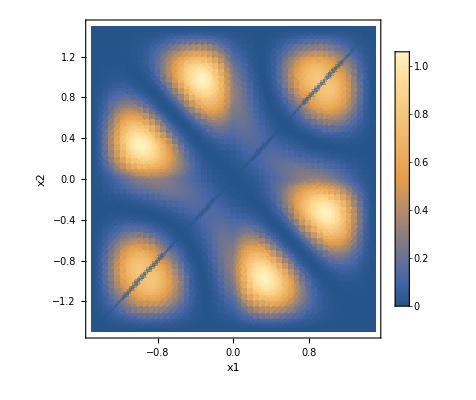

```mathematica
DensityPlot[2 Abs[(WFFULL[xx1,xx2]/(1Sqrt[WF2Norm]))]^2/.HeavisideTheta[0]->1, {xx1, -intRange, intRange}, {xx2, -intRange, intRange}, FrameLabel->{"x1", "x2"}, PlotLegends->Automatic,PlotRange->Full, PlotPoints->50]
```